```mathematica
(*Coulomb Potential*)
V[r_]=-14.3996448504451555789912633575295935414`6.88249108029756/r;α=0.26246843532124502683678435500618410715`6.076375074285658;
a=0.52917721036724619261935939416491622623`6.45296897443304;
```

```mathematica
(*V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;α=2.;*)
```

```mathematica
(*Variable substitution*)
Clear[f,r,ξ,ψ];
radialEq=V[r] f[r]-f''[r]/α
radialξ=Simplify[radialEq/.f->(ψ[ArcTan[#]]&)/.r->(Tan[ξ]),Pi/2>ξ>0]
```

-(14.3996 f[r])/r-3.80998 f''[r]

-14.4 Cot[ξ] ψ[ξ]+(7.62 Tan[ξ] ψ'[ξ]-3.81 ψ''[ξ])/((1.+Tan[ξ]^2)^2)

```mathematica
(*Analytic solution*)
R[n_,r_]=FullSimplify[2/(a^(3/2) n^2 (2 l+1)!) Sqrt[(n+l)!/(n-l-1)!] E^(-1/2 (2 r)/(n a)) ((2 r)/(n a))^l Hypergeometric1F1[-n+l+1,2 l+2,(2 r)/(n a)]];
u[n_,r_]=r R[n,r]/.l->0
```

(5.19551 ⅇ^(-(1.88973 r)/n) r √(Gamma[1+n]/Gamma[n]) Hypergeometric1F1[1-n,2,(3.77945 r)/n])/n^2

```mathematica
With[{max=20,shift=20},{ev,ef}=NDEigensystem[{radialξ+shift ψ[ξ],DirichletCondition[ψ[ξ]==0,True]},ψ,{ξ,0,Pi/2},max,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->40000}}];
evNew=ev-shift]
```

{-13.6057,-3.40142,-1.51174,-0.850356,-0.544228,-0.377936,-0.277667,-0.212588,-0.167969,-0.13605,-0.112427,-0.0944449,-0.0804237,-0.0692623,-0.0601369,-0.0524875,-0.0468007,-0.0402104,-0.0350137,-0.0310644}

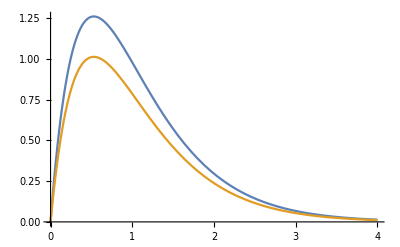
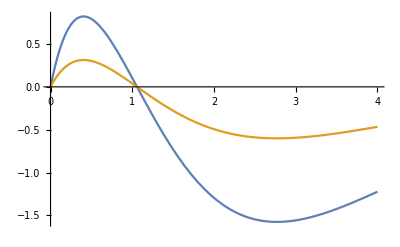
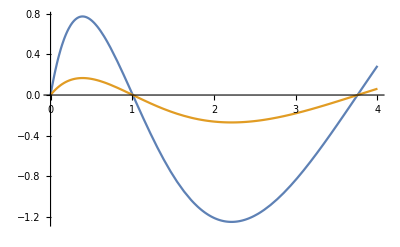
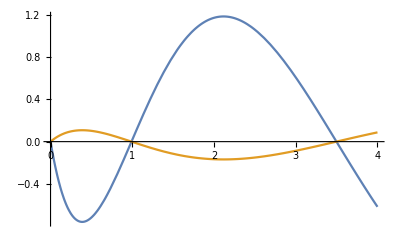
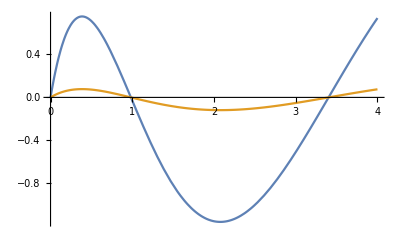
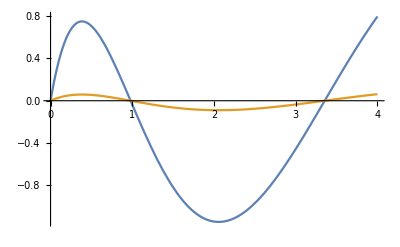

```mathematica
(*This is the first time I tried to compare these two.I forgot I needed to do the normalization mannally.*)
Table[Plot[{(-1)^n ef[[n]][ξ]/.ξ->ArcTan[r],u[n,r]},{r,0,4}],{n,6}]
```

```mathematica
(*It's my verification for the energy.It looks good.*)
%%-{-13.60569251616784198966339492781954713122`6.883220831107512,-3.4014231290419604974158487319548867828`6.883220831107512,-1.51174361290753799885148832531328301458`6.883220831107512,-0.8503557822604901243539621829887216957`6.883220831107512,-0.54422770064671367958653579711278188525`6.883220831107512,-0.37793590322688449971287208132832075364`6.883220831107512,-0.27766719420750697938088561077182749247`6.883220831107512,-0.21258894556512253108849054574718042393`6.883220831107512,-0.16797151254528199987238759170147589051`6.883220831107512,-0.13605692516167841989663394927819547131`6.883220831107512,-0.11244373980304001644349913163487229034`6.883220831107512,-0.09448397580672112492821802033208018841`6.883220831107512,-0.08050705630868545556013843152555945048`6.883220831107512,-0.06941679855187674484522140269295687312`6.883220831107512,-0.06046974451630151995405953301253132058`6.883220831107512,-0.05314723639128063277212263643679510598`6.883220831107512,-0.04707852081718976467011555338345864059`6.883220831107512,-0.04199287813632049996809689792536897263`6.883220831107512,-0.03768889893675302490211466739008184801`6.883220831107512,-0.03401423129041960497415848731954886783`6.883220831107512}
```

{-1.69049×10^-6,-1.06595×10^-7,-2.98519×10^-8,-1.26476×10^-8,-6.59775×10^-9,-3.91585×10^-9,-2.53588×10^-9,-1.74807×10^-9,-1.26334×10^-9,-9.47164×10^-10,-7.31437×10^-10,-5.78535×10^-10,-4.66632×10^-10,-3.82205×10^-10,-3.16485×10^-10,-2.6334×10^-10,-2.17797×10^-10,-1.72412×10^-10,-4.64763×10^-10,4.21613×10^-9}

```mathematica
ef
```

{InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}}, <>]}

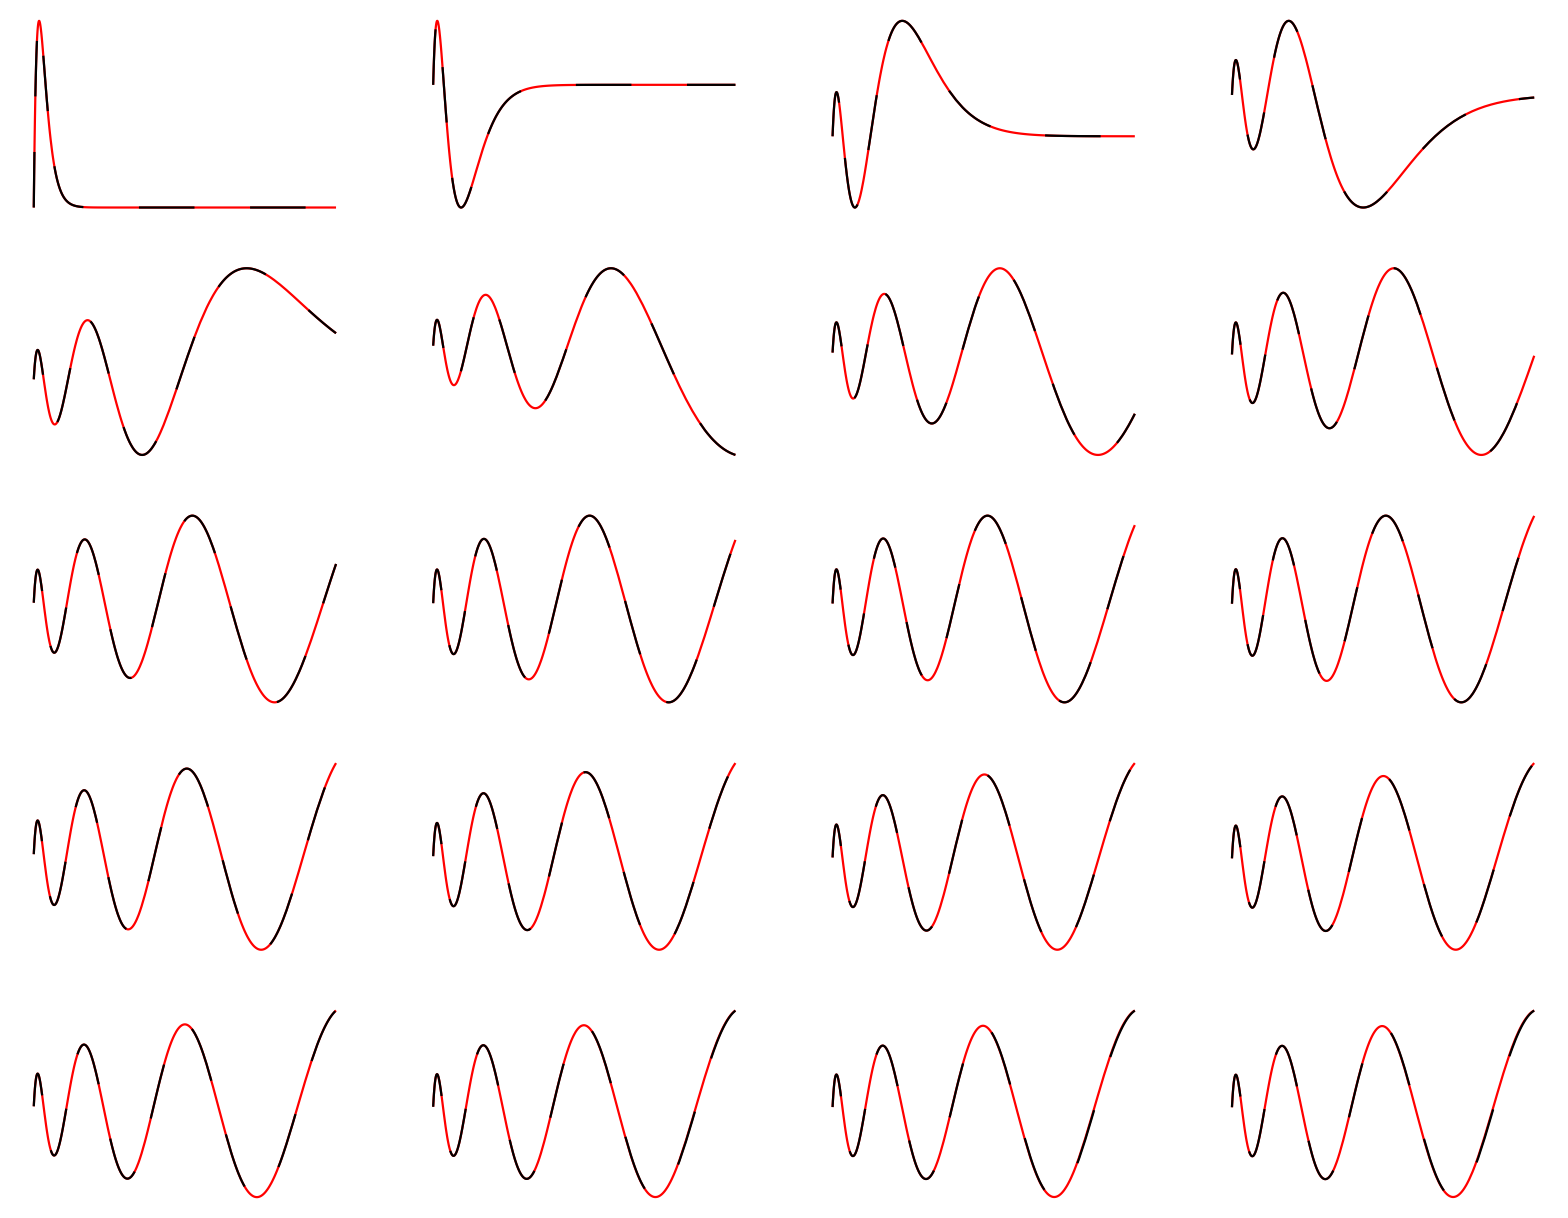

```mathematica
(*It's the code from the guy told me about variable substitution.He use the limit of r=0 to match the amplitude of two functions.*)
Needs["NumericalCalculus`"]

amplitudes=Table[NLimit[u[i,r]/ef[[i]][ArcTan[r]],r->0],{i,Length[ef]}];

GraphicsGrid@Partition[Table[Plot[{amplitudes[[i]] ef[[i]][ArcTan[r]],u[i,r]},{r,0,30},Frame->None,Axes->None,PlotRange->All,PlotStyle->{Red,Directive[Black,Dashing[.1]]}],{i,Length[ef]}],4]
```

```mathematica
(*I arbitrary choose a point to fit it.*)
amplitude=Table[u[i,r]/ef[[i]][ArcTan[r]]/.r->0.1,{i,20}]
```

{0.803368,0.381182,0.216035,0.1421,-0.102244,-0.0780081,-0.062012,-0.0508129,0.0426164,-0.0364065,0.0315699,0.0277168,0.0245893,-0.0220136,-0.0198692,-0.0179648,0.0165622,-0.0155898,-0.0139743,-0.0128138}

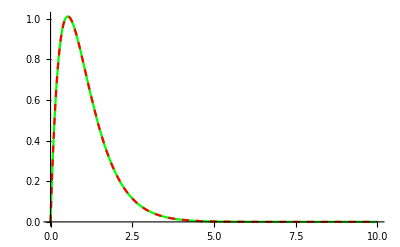
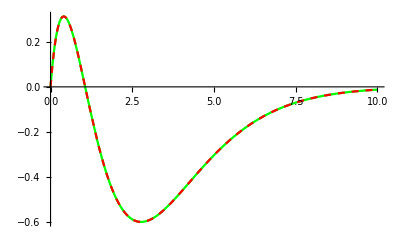
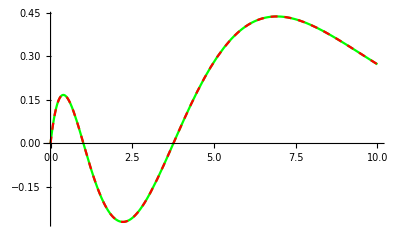
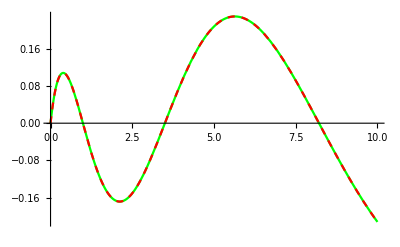
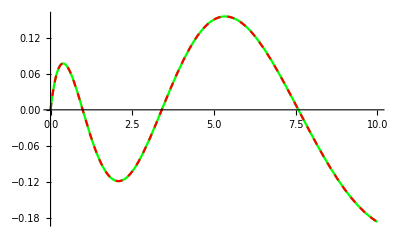
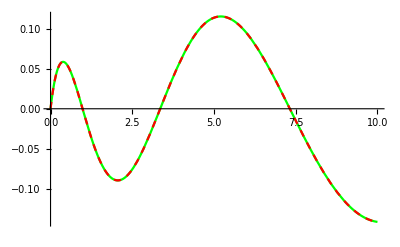
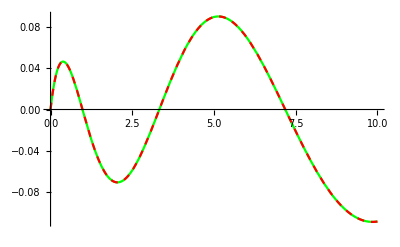
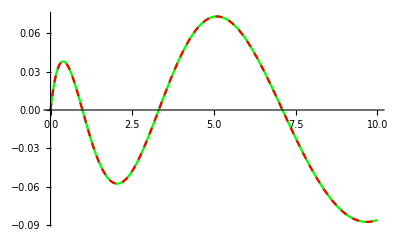

```mathematica
(*The result seems fine*)
Table[Plot[{amplitude[[i]]ef[[i]][ArcTan[r]],u[i,r]},{r,0,10},PlotStyle->{Green,Directive[Dashed,Red]}],{i,20}]
```

```mathematica
Table[NIntegrate[(amplitude[[i]]ef[[i]][ArcTan[r]])^2,{r,0,∞}],{i,5}]
```

{1.,1.,1.,1.,1.}

```mathematica
(*I tried to use NIntegrate here in case we don't have a analytic solution*)
am=Table[NIntegrate[(ef[[i]][ArcTan[r]])^2,{r,0,∞}],{i,5}]^(-1/2)
```

{0.803368,0.381182,0.216035,0.1421,0.102244}

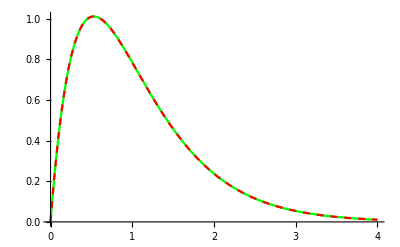
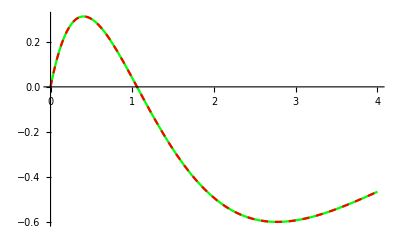
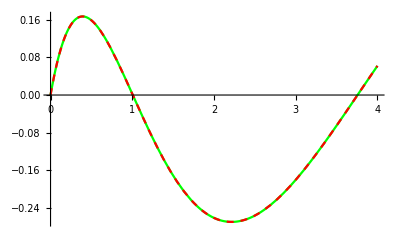
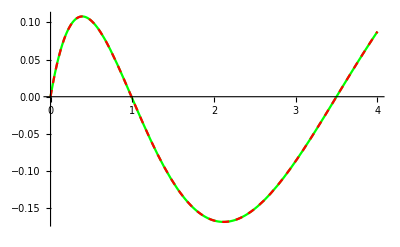
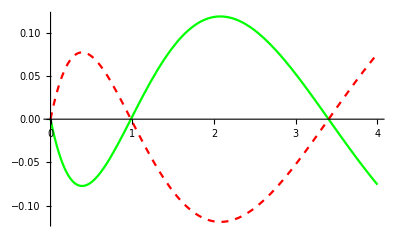

```mathematica
Table[Plot[{am[[i]]ef[[i]][ArcTan[r]],u[i,r]},{r,0,4},PlotStyle->{Green,Directive[Dashed,Red]}],{i,5}]
```

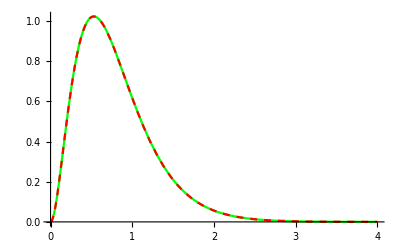
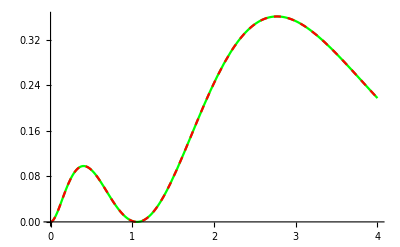
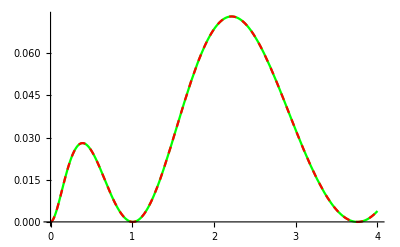
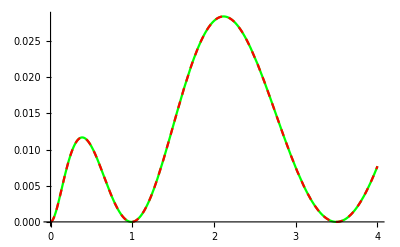
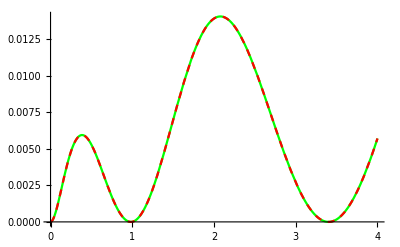

```mathematica
(*The last one seems to have some sign problem,so I tried to compare the square of them.*)
Table[Plot[{(am[[i]]ef[[i]][ArcTan[r]])^2,u[i,r]^2},{r,0,4},PlotStyle->{Green,Directive[Dashed,Red]}],{i,5}]
```

```mathematica
(*When n becomes greater,it's harder for NIntegrate to converge.So far I still can't solve this problem.So I reduce the integrate limit to get a relatively fine result.*)
```

```mathematica
NIntegrate[(ef[[6]][ArcTan[r]])^2,{r,0,2000}(*,Method->"ClenshawCurtisRule"*)]
```

NIntegrate::ncvb: 在接近 {r} = {13.7799} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 164.328 和 0.0128163.

164.328

```mathematica
(*It only differ lightly from the analytic result in 150 angstrom away and only have a scale of 10E-21,so I assume it's a reliable result.*)
```

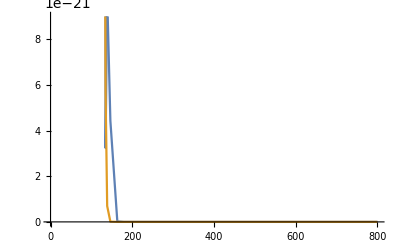

```mathematica
Plot[{((%72)^-0.5 ef[[6]][ArcTan[r]])^2,u[6,r]^2},{r,0,800}]
```